```mathematica
probs=Solve[60 x^3-60 x^2+15x-1==0][[;;,1,2]]
```

{Root0.109Root[-1+15 #1-60 #1^2+60 #1^3&,1]0.10903900907287718,Root0.232Root[-1+15 #1-60 #1^2+60 #1^3&,2]0.23193336855303062,Root0.659Root[-1+15 #1-60 #1^2+60 #1^3&,3]0.6590276223740922}

```mathematica
amplitudes=Table[RotateRight[√N[probs],i],{i,0,2}]
```

{{0.330211,0.481595,0.811805},{0.811805,0.330211,0.481595},{0.481595,0.811805,0.330211}}

```mathematica
basis=amplitudes {{1,1,1},{1,Exp[I x[1]],Exp[I x[2]]},{1,Exp[I x[3]],Exp[I x[4]]}}
```

{{0.330211,0.481595,0.811805},{0.811805,0.330211 ⅇ^(ⅈ x[1]),0.481595 ⅇ^(ⅈ x[2])},{0.481595,0.811805 ⅇ^(ⅈ x[3]),0.330211 ⅇ^(ⅈ x[4])}}

```mathematica
phases=Chop[Solve[#==0&/@DeleteCases[Flatten[#.(#ᵀ/.x[i_]:>-x[i])&[basis]],1.]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[1]→-5.42433,x[2]→3.45464,x[3]→-2.59578,x[4]→0.858851},{x[1]→5.42433,x[2]→-3.45464,x[3]→2.59578,x[4]→-0.858851}}

```mathematica
basisSol= basis/.phases[[1]]
```

{{0.330211,0.481595,0.811805},{0.811805,0.215729+0.25 ⅈ,-0.458189-0.14831 ⅈ},{0.481595,-0.693857-0.421415 ⅈ,0.215729+0.25 ⅈ}}

```mathematica
unitary=basisSol.DiagonalMatrix[Exp[I{x,y,z}]].basisSol†;
```

```mathematica
t=3
Monitor[Do[Do[Module[{tmpUnit=unitary/.{x->i[[1]],y->i[[2]],z->i[[3]]},states,welch},
states=Flatten[Table[MatrixPower[tmpUnit,j]ᵀ,{j,0,k}],1];
welch=1/Length[states]^2 Total[Chop[Abs[#.#†]^(2t)&[states]],2]-Binomial[3+t-1,t]^-1;
If[welch==0,Print[i]]],{i,2Pi #/(k+1)&[DeleteDuplicatesBy[Tuples[Range[k],{3}],Sort]]}],{k,3,25}],{i,k}]
```

3

```mathematica
list={}
nBases=63
Monitor[Do[Module[{tmpUnit=unitary/.{x->RandomReal[2Pi],y->RandomReal[2Pi],z->RandomReal[2Pi]},states,welch},
states=Flatten[Table[MatrixPower[tmpUnit,j]ᵀ,{j,0,nBases}],1];
welch=1/Length[states]^2 Total[Chop[Abs[#.#†]^(2t)&[states]],2]-Binomial[3+t-1,t]^-1;
AppendTo[list,welch];
If[welch==0,Print[i]]],10000],Length[list]]
```

{}

63

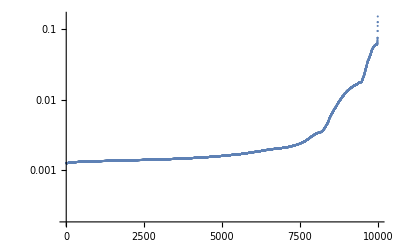

```mathematica
ListLogPlot[list//Sort,PlotRange->{Full,{0,Full}}]
```